```mathematica
(*Subscript[f, column]*)
Nn= 4;
Manipulate[Grid@Table[Subscript[c, n] e^(i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],{nmax,0,Nn-1},{kmax,0,Nn-1}]
```

```mathematica
(*Subscript[c, row]*)
Manipulate[Grid@Join[
Table[Subscript[f, k] e^(-i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],
Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}]
],{nmax,0,Nn-1},{kmax,0,Nn-1}]
(*Manipulate[Grid@Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}],{nmax,0,3},{kmax,0,3}]*)
```

```mathematica
dft[f_List]:= With[{t=Length[f]},Table[Total@Table[f[[k+1]]Exp[-(ⅈ 2π n k)/t],{k,0,t-1}],{n,0,t-1}]]
dft[{0,1,4,9}]
```

{14,-4+8 ⅈ,-6,-4-8 ⅈ}

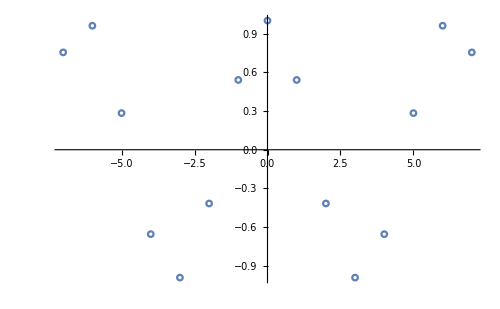

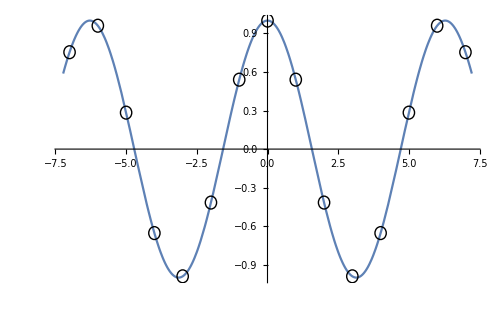

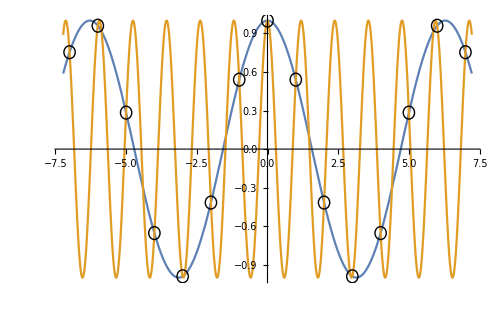

```mathematica
points1 = Join[{PointSize[0.03]},Table[{Red,Point[{i,Cos[i]}]},{i,-7,7}]];
points2 = Join[{PointSize[0.02]},Table[{Black,Point[{i,Cos[(2π-1)i]}]},{i,-7,7}]];
(*ListPlot[{pointsA,pointsB,pointsS},ImageSize->500,PlotMarkers->{{Graphics@Circle[{0,0},1],0.05}}]*)
(*Plot[{Cos[t],Cos[(2π-1)t]},{t,-2.3π,2.3π},Epilog->Join[points1,points2]]*)
(*Plot[Cos[t],{t,-3π,3π},
Epilog->Table[Circle[{i,Cos[i]},{0.2,0.05}], {i,-7,7,1}],ImageSize->500]
Plot[{Cos[t],Cos[(2π-1)t]},{t,-2π,2π},
Epilog->Table[Circle[{i,Cos[i]},{0.2,0.05}], {i,-7,7,1}],ImageSize->500]*)
(*ListPlot[points]*)
(*Plot[{Cos[t]},{t,-1.7π,1.7π},Epilog->points,ImageSize->500]*)
circles = Table[Circle[{i,Cos[i]},{0.2,0.05}],{i,-7,7}];
points = Table[{i,Cos[i]},{i,-7,7}];
ListPlot[points,ImageSize->500,PlotMarkers->{Graphics@Circle[{0,0},0.5],0.05}]
Plot[Cos[t],{t,-2.3π,2.3π},Epilog->circles,ImageSize->500]
Plot[{Cos[t],Cos[(2π-1)t]},{t,-2.3π,2.3π},Epilog->circles,ImageSize->500]
```

```mathematica
2Fourier[{0,1,4,9}]
```

{14.+0. ⅈ,-4.-8. ⅈ,-6.+0. ⅈ,-4.+8. ⅈ}

```mathematica
fft[{x_,y_},n_] := x+y Exp[-ⅈ π n ]
fft[f_List,n_]:=fft[Downsample[f,2,1],n]+Exp[-(ⅈ 2π n)/Length[f]]fft[Downsample[f,2,2],n]
fft[f_List]:= Table[fft[f,n]//N,{n,0,Length[f]-1}]
fft[{0,1,4,9}]
fft[{1,0},0]
fft[{4,9},0]
```

{14.,-4.+8. ⅈ,-6.,-4.-8. ⅈ}

1

13

{{-102.4,1.×10^6},{-102.3,1.×10^6},{-102.2,1.×10^6},{-102.1,1.×10^6},{-102.,1.×10^6},{-101.9,1.×10^6},{-101.8,1.×10^6},{-101.7,1.×10^6},{-101.6,1.×10^6},{-101.5,1.×10^6}}

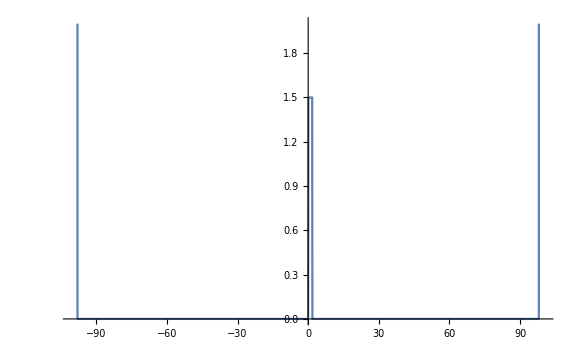

```mathematica
Take[dataV, 10]
(*ListLinePlot[dataV, PlotRange->{{-100,100},{0,2}}, ImageSize->Large]*)
```

```mathematica
Take[dataC, 10]
(*Manipulate[ListLinePlot[Take[dataC, {2*i-1,2*i}],PlotRange->{{-100,100},{0,2}}], {i, 1,Length@dataC/2, 1}]*)
```

{{-34.4474,0.},{-34.4474,1.},{-34.2537,0.},{-34.2537,1.},{-34.0601,0.},{-34.0601,1.},{-33.8664,0.},{-33.8664,1.},{-33.6728,0.},{-33.6728,1.}}

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Take[dataX, 10]
nt = Length@dataC/2;
nx = Length@dataX/nt
(*Manipulate[ListLinePlot[Take[dataX, {nx*i+1,nx*(i+1)}],PlotRange->{{-100,100},{0,2}}, ImageSize->Large], {i, 0,nt-1, 1}]*)
```

{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.}}

2048

Take::normal: Nonatomic expression expected at position 1 in Take[dataX,{1+381 nx,382 nx}].

ListLinePlot::lpn: Take[dataX,{1+381 nx,382 nx}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.},{-101.4,0.},{-101.3,0.},{-101.2,0.},{-101.1,0.},{-101.,0.},«22»,{-98.7,0.},{-98.6,0.},{-98.5,0.},{-98.4,0.},{-98.3,0.},{-98.2,0.},{-98.1,0.},{-98.,0.},{-97.9,0.},{-97.8,0.},{-97.7,0.},{-97.6,0.},{-97.5,0.},«942030»},«1»].

$Aborted[]

ListLinePlot::lpn: Take[{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.},{-101.4,0.},{-101.3,0.},{-101.2,0.},{-101.1,0.},{-101.,0.},«22»,{-98.7,0.},{-98.6,0.},{-98.5,0.},{-98.4,0.},{-98.3,0.},{-98.2,0.},{-98.1,0.},{-98.,0.},{-97.9,0.},{-97.8,0.},{-97.7,0.},{-97.6,0.},{-97.5,0.},«942030»},«1»] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Take[dataK, 10]
nt = Length@dataC/2;
nk = Length@dataK/nt
(*Manipulate[ListLinePlot[Take[dataK, {nk*i+1,nk*(i+1)}],PlotRange->{{-10,10},{0,3}}, ImageSize->Large], {i, 0,nt-1, 1}]*)
```

{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.}}

2048

Take::normal: Nonatomic expression expected at position 1 in Take[dataK,{1+206 nk,207 nk}].

ListLinePlot::lpn: Take[dataK,{1+206 nk,207 nk}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.},{-27.6932,0.},{-27.6625,0.},«27»,{-26.8035,0.},{-26.7728,0.},{-26.7421,0.},{-26.7115,0.},{-26.6808,0.},{-26.6501,0.},{-26.6194,0.},{-26.5887,0.},{-26.5581,0.},{-26.5274,0.},{-26.4967,0.},«942030»},{1+206 nk,207 nk}].

ListLinePlot::lpn: Take[{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.},{-27.6932,0.},{-27.6625,0.},«27»,{-26.8035,0.},{-26.7728,0.},{-26.7421,0.},{-26.7115,0.},{-26.6808,0.},{-26.6501,0.},{-26.6194,0.},{-26.5887,0.},{-26.5581,0.},{-26.5274,0.},{-26.4967,0.},«942030»},{1+206 nk,207 nk}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

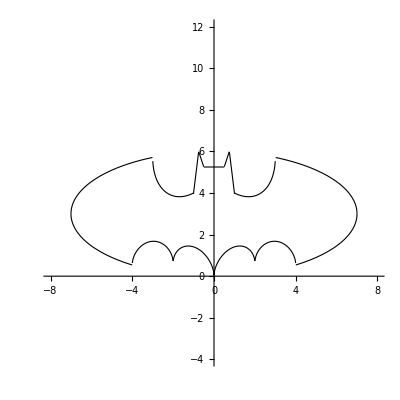

```mathematica
f1 [x_]:= 3 √(-(x/7)^2+1)
f2[x_]:=-f1[x]
f3 [x_]:= Abs@(x/2)-(3 √33-7)/112 x^2+√(1-(Abs[Abs@x-2]-1)^2)-3
f4[x_]:=9-8Abs@x
f5[x_]:=3Abs@x+.75
f6[x_]:=2.25
f7[x_]:=1.5-.5Abs@x-(6 √10)/14(√(3-x^2+2Abs@x)-2)
Plot[
{
Piecewise[{
{3+f1[x],Abs@x≥3.01}, 
{3+f4[x], 0.75≤ Abs@x≤ 1.01},
{3+f5[x], .5≤ Abs@x≤ .75},
{3+f6[x], Abs@x≤ .5},
{3+f7[x],Abs@x≥ 1}}],
Piecewise[{
{3+f2[x],Abs@x≥ 4},
{3+f3[x],Abs@x≤ 4}}]
},
{x,-7,7},
PlotRange->{{-8,8},{-4,12}},
PlotStyle->{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},
AspectRatio->Full]
battop[x_]:=Piecewise[{
{3+f1[x],Abs@x≥3.01}, 
{3+f4[x], 0.75≤ Abs@x≤ 1.01},
{3+f5[x], .5≤ Abs@x≤ .75},
{3+f6[x], Abs@x≤ .5},
{3+f7[x],Abs@x≥ 1}}]
```

```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/QuantumPython/";dataX = Import[path <> "QuantumPythonX.txt", "Data"];
dataK = Import[path <> "QuantumPythonK.txt", "Data"];
dataV = Import[path <> "QuantumPythonV.txt", "Data"];
dataC = Import[path <> "QuantumPythonC.txt", "Data"];
```

```mathematica
nt = Length@dataC/2;
n = Length@dataK/nt;
m = 1.;
V0 = 1.5;
p0=Sqrt[2m 0.4V0];
sqrt2mV0= Sqrt[2m V0];
battoppts=Table[{i,battop@i-0.1},{i,Range[-7,7,0.01]}];
plotX[t_] := ListLinePlot[
{
Take[dataX, {n*(t-1)+1,n*t}],
dataV,
Take[dataC, {2*t-1,2*t}](*,
battoppts*)
},
PlotStyle->
{
{Red},
{Black,Thickness[0.002]},
{Black,Dotted}(*,
{Black,Thickness[0.002]}*)
},
PlotRange->{{-100,100},{0,2}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ(x)|","V(x)","x_0+v_0t"},
AxesLabel->{"x","|ψ(x)|"},
AxesOrigin->{-100,0},
PlotRangePadding->{{0.1,0.2},{0.01,0}}(*,
AspectRatio->1/8*)]
plotK[t_] := ListLinePlot[
{
Take[dataK, {n*(t-1)+1,n*t}],
{{-p0,0},{-p0,3}},
{{p0,0},{p0,3}},
{{sqrt2mV0,0},{sqrt2mV0,3}}
},
PlotStyle->
{
{Red},
{Black,Dotted},
{Black,Dashed},
{Black,Dotted}
},
PlotRange->{{-4,4},{0,2.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ^─(k)|","±p0","√(2 SubscriptBox[mV, 0])"},
AxesLabel->{"x","|ψ^─(k)|"},
AxesOrigin->{-4,0},
PlotRangePadding->{0,0.01}(*,
AspectRatio->1/8*)]
```

```mathematica
plotsX = Table[plotX[t],{t, 1,nt, 1}];
plotsK = Table[plotK[t],{t, 1,nt, 1}];
```

```mathematica
Manipulate[Column@{plotX[t],plotK[t]},{t, 1,nt,1, AnimationRate->10}]
(*Manipulate[Column@{plotsX[[Round[100*t]]],plotsK[[Round[100*t]]]},{t, 0.01,nt/100, 0.01, AnimationRate -> 8}]*)
(*Manipulate[Round[10*t],{t, 0.1,10*nt, 0.1}]*)
```

```mathematica
nt
```

460

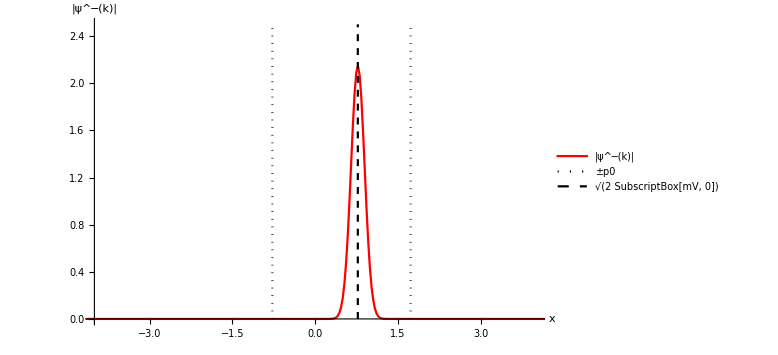

```mathematica
ListLinePlot[
{
Take[dataK, {nx*(1-1)+1,nx*1}],
{{-p0,0},{-p0,3}},
{{p0,0},{p0,3}},
{{sqrt2mV0,0},{sqrt2mV0,3}}
},
PlotStyle->
{
{Red},
{Black,Dotted},
{Black,Dashed},
{Black,Dotted}
},
PlotRange->{{-4,4},{0,2.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ^─(k)|","±p0","√(2 SubscriptBox[mV, 0])"},
AxesLabel->{"x","|ψ^─(k)|"},
AxesOrigin->{-4,0},
PlotRangePadding->{0,0.01}]
```

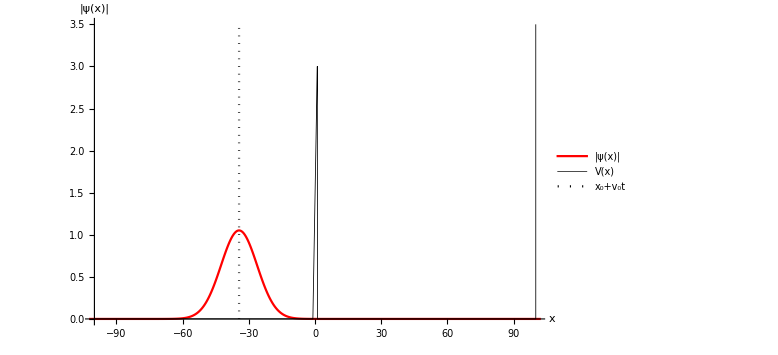

```mathematica
ListLinePlot[
{
Take[dataX, {nx*(1-1)+1,nx*1}],
dataV,
Take[dataC, {2*1-1,2*1}]
},
PlotStyle->
{
{Red},
{Black,Thickness[0.002]},
{Black,Dotted}
},
PlotRange->{{-100,100},{0,3.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ(x)|","V(x)","x_0+v_0t",""},
AxesLabel->{"x","|ψ(x)|"},
AxesOrigin->{-100,0},
PlotRangePadding->{{0.1,0.2},{0.01,0}}
]
```

```mathematica
dft[ts_List,fs_List]:= (
l=Length[ts]; 
dt=Abs@ts[[2]]-Abs@ts[[1]]//Abs;
w0 = -π/dt;
ws=Array[#&,l,{-Abs@w0,Abs@w0}];
dw=Abs@ws[[2]]-Abs@ws[[1]]//Abs;
t0=ts[[1]] ;
gs=Table[Total@Table[fs[[k+1]]Exp[-ⅈ (w0+n*dw)(t0+k*dt)],{k,0,l-1}],{n,0,l-1}]/Sqrt[l-1];
(*gs = Exp[-ⅈ*Outer[Times,ws,ts]].fs/Sqrt[l-1];*)
grpts = Riffle[ws//N,Re@gs//N]~Partition~2;
gipts = Riffle[ws//N,Im@gs//N]~Partition~2;
fpts = Riffle[ts//N,fs//N]~Partition~2;
{fpts,grpts,gipts}
(*ListLinePlot[{fpts,gpts},PlotRange->Full,ImageSize->Large]*)
)
gaussian[t_, m_, s_]:=Exp[-(t-m)^2/(2 s^2)];
t0 = -30;
l=2^10;
ts=Array[#&,l,{-Abs@t0,Abs@t0}];
gdatasimple = dft[ts,Table[gaussian[t, 0, 0.5],{t,ts}]];
```

```mathematica
gdatasimple1 = dft[ts,Table[gaussian[t, 0, 0.5],{t,ts}]];
gdatasimple2 = dft[ts,Table[gaussian[t, 0, 2],{t,ts}]];
gdatasimple3 = dft[ts,Table[gaussian[t, 1, 2],{t,ts}]];
```

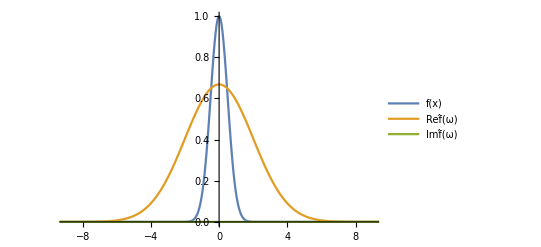

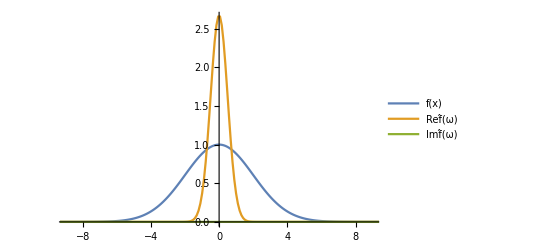

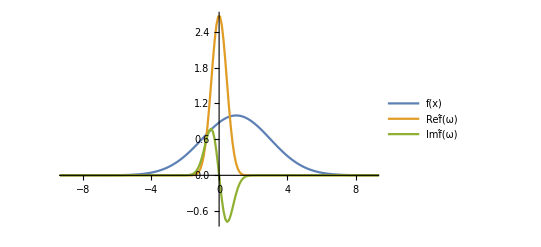

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/gaussian1.pdf

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/gaussian2.pdf

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/gaussian3.pdf

```mathematica
size = Full;
a=ListLinePlot[gdatasimple1,PlotRange->{{-9,9},Full},PlotLegends->{"f(x)","Ref̂(ω)","Imf̂(ω)"},ImageSize->size]
b=ListLinePlot[gdatasimple2,PlotRange->{{-9,9},Full},PlotLegends->{"f(x)","Ref̂(ω)","Imf̂(ω)"},ImageSize->size]
c=ListLinePlot[gdatasimple3,PlotRange->{{-9,9},Full},PlotLegends->{"f(x)","Ref̂(ω)","Imf̂(ω)"},ImageSize->size]
otherpath = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/";
Export[otherpath<>"gaussian1.pdf",a]
Export[otherpath<>"gaussian2.pdf",b]
Export[otherpath<>"gaussian3.pdf",c]
```

```mathematica
gdata= Table[dft[ts,Table[gaussian[t, m, s],{t,ts}]],{m,-1,1,1},{s,0.5,2,0.5}];
```

$Aborted

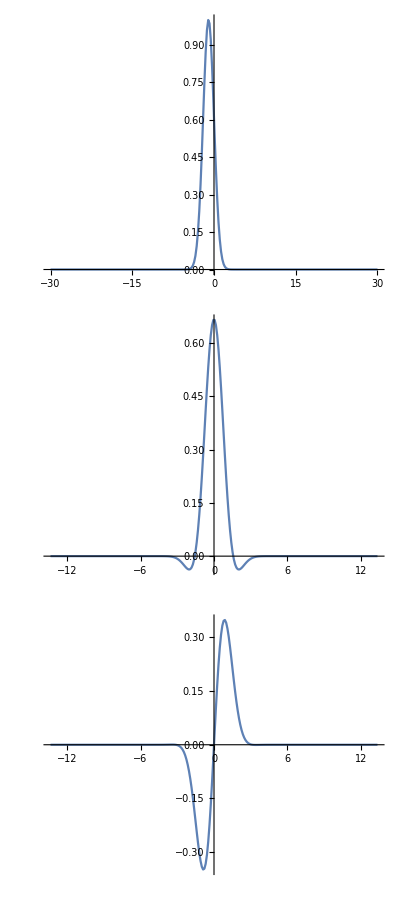

```mathematica
Column@Table[ListLinePlot[gdata[[1]][[2]][[i]],PlotRange->Full, ImageSize->Medium],{i,1,3,1}]
```

```mathematica
Manipulate[ListLinePlot[gdata[[m+2]][[Round[2*s]]],PlotRange->Full,ImageSize->Large],{m,-1,1,1},{s,0.5,2,0.5}]
```

Part::partd: Part specification gdata⟦3⟧ is longer than depth of object.

ListLinePlot::lpn: gdata is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partd: Part specification gdata⟦3⟧ is longer than depth of object.

ListLinePlot::lpn: gdata is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partd: Part specification gdata⟦3⟧ is longer than depth of object.

ListLinePlot::lpn: gdata is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partd: Part specification gdata⟦3⟧ is longer than depth of object.

ListLinePlot::lpn: gdata is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
osc[t_]:=Sin[10t]Exp[-t];
l=2^8;
ts=Array[#&,l,{0,10}];
odata=dft[ts,osc/@ts];
```

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/osch.pdf

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/oschre.pdf

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/oschim.pdf

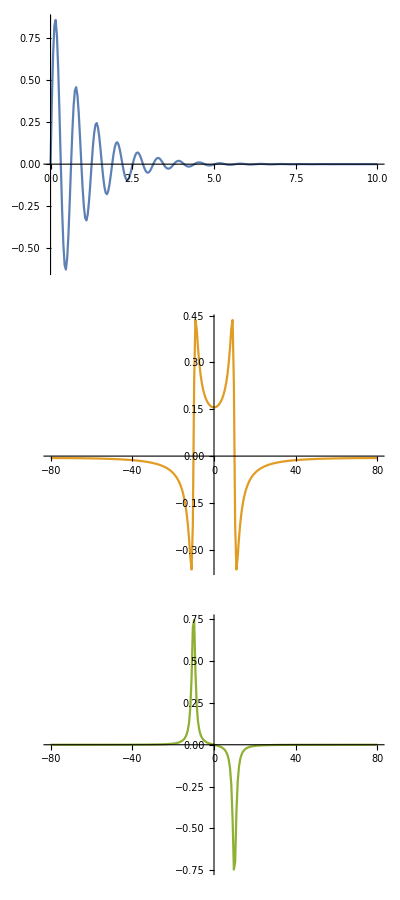

```mathematica
colors=ColorData[97,"ColorList"];
plots = Table[ListLinePlot[odata[[i]],PlotRange->Full, PlotStyle-> colors[[i]],ImageSize->Full],{i,1,3,1}];
Export[otherpath<>"osch.pdf",plots[[1]]]
Export[otherpath<>"oschre.pdf",plots[[2]]]
Export[otherpath<>"oschim.pdf",plots[[3]]]
Column@plots
```

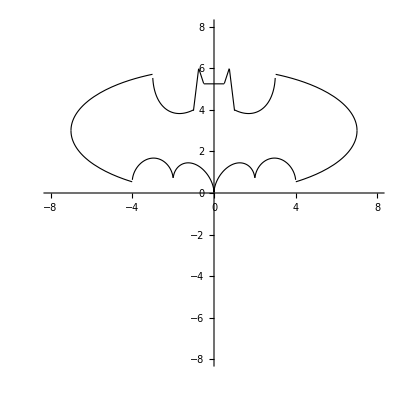

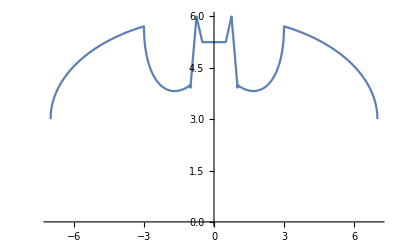

```mathematica
ListLinePlot[odata[[i]],PlotRange->Full, ImageSize->Full]
```

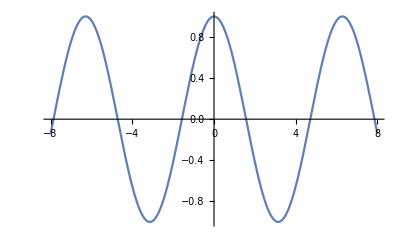

```mathematica
(*t=Array[#&,800,{-2.3π,2.3π}];*)
Clear[t]
Plot[Cos[t],{t,-8,8},PlotRange->{{-8,8},{-1,1}}]
Plot[Cos[t],{t,-8,8},PlotRange->{{-8,8},{-1,1}}]
```

```mathematica
Range[-8,8,4.6π/801]
```

{-8.,-7.98196,-7.96392,-7.94588,-7.92783,-7.90979,-7.89175,-7.87371,-7.85567,-7.83763,-7.81958,-7.80154,-7.7835,-7.76546,-7.74742,-7.72938,-7.71133,-7.69329,-7.67525,-7.65721,-7.63917,-7.62113,-7.60308,-7.58504,-7.567,-7.54896,-7.53092,-7.51288,-7.49484,-7.47679,-7.45875,-7.44071,-7.42267,-7.40463,-7.38659,-7.36854,-7.3505,-7.33246,-7.31442,-7.29638,-7.27834,-7.26029,-7.24225,-7.22421,-7.20617,-7.18813,-7.17009,-7.15204,-7.134,-7.11596,-7.09792,-7.07988,-7.06184,-7.04379,-7.02575,-7.00771,-6.98967,-6.97163,-6.95359,-6.93555,-6.9175,-6.89946,-6.88142,-6.86338,-6.84534,-6.8273,-6.80925,-6.79121,-6.77317,-6.75513,-6.73709,-6.71905,-6.701,-6.68296,-6.66492,-6.64688,-6.62884,-6.6108,-6.59275,-6.57471,-6.55667,-6.53863,-6.52059,-6.50255,-6.48451,-6.46646,-6.44842,-6.43038,-6.41234,-6.3943,-6.37626,-6.35821,-6.34017,-6.32213,-6.30409,-6.28605,-6.26801,-6.24996,-6.23192,-6.21388,-6.19584,-6.1778,-6.15976,-6.14171,-6.12367,-6.10563,-6.08759,-6.06955,-6.05151,-6.03346,-6.01542,-5.99738,-5.97934,-5.9613,-5.94326,-5.92522,-5.90717,-5.88913,-5.87109,-5.85305,-5.83501,-5.81697,-5.79892,-5.78088,-5.76284,-5.7448,-5.72676,-5.70872,-5.69067,-5.67263,-5.65459,-5.63655,-5.61851,-5.60047,-5.58242,-5.56438,-5.54634,-5.5283,-5.51026,-5.49222,-5.47418,-5.45613,-5.43809,-5.42005,-5.40201,-5.38397,-5.36593,-5.34788,-5.32984,-5.3118,-5.29376,-5.27572,-5.25768,-5.23963,-5.22159,-5.20355,-5.18551,-5.16747,-5.14943,-5.13138,-5.11334,-5.0953,-5.07726,-5.05922,-5.04118,-5.02314,-5.00509,-4.98705,-4.96901,-4.95097,-4.93293,-4.91489,-4.89684,-4.8788,-4.86076,-4.84272,-4.82468,-4.80664,-4.78859,-4.77055,-4.75251,-4.73447,-4.71643,-4.69839,-4.68034,-4.6623,-4.64426,-4.62622,-4.60818,-4.59014,-4.57209,-4.55405,-4.53601,-4.51797,-4.49993,-4.48189,-4.46385,-4.4458,-4.42776,-4.40972,-4.39168,-4.37364,-4.3556,-4.33755,-4.31951,-4.30147,-4.28343,-4.26539,-4.24735,-4.2293,-4.21126,-4.19322,-4.17518,-4.15714,-4.1391,-4.12105,-4.10301,-4.08497,-4.06693,-4.04889,-4.03085,-4.01281,-3.99476,-3.97672,-3.95868,-3.94064,-3.9226,-3.90456,-3.88651,-3.86847,-3.85043,-3.83239,-3.81435,-3.79631,-3.77826,-3.76022,-3.74218,-3.72414,-3.7061,-3.68806,-3.67001,-3.65197,-3.63393,-3.61589,-3.59785,-3.57981,-3.56176,-3.54372,-3.52568,-3.50764,-3.4896,-3.47156,-3.45352,-3.43547,-3.41743,-3.39939,-3.38135,-3.36331,-3.34527,-3.32722,-3.30918,-3.29114,-3.2731,-3.25506,-3.23702,-3.21897,-3.20093,-3.18289,-3.16485,-3.14681,-3.12877,-3.11072,-3.09268,-3.07464,-3.0566,-3.03856,-3.02052,-3.00248,-2.98443,-2.96639,-2.94835,-2.93031,-2.91227,-2.89423,-2.87618,-2.85814,-2.8401,-2.82206,-2.80402,-2.78598,-2.76793,-2.74989,-2.73185,-2.71381,-2.69577,-2.67773,-2.65968,-2.64164,-2.6236,-2.60556,-2.58752,-2.56948,-2.55144,-2.53339,-2.51535,-2.49731,-2.47927,-2.46123,-2.44319,-2.42514,-2.4071,-2.38906,-2.37102,-2.35298,-2.33494,-2.31689,-2.29885,-2.28081,-2.26277,-2.24473,-2.22669,-2.20864,-2.1906,-2.17256,-2.15452,-2.13648,-2.11844,-2.10039,-2.08235,-2.06431,-2.04627,-2.02823,-2.01019,-1.99215,-1.9741,-1.95606,-1.93802,-1.91998,-1.90194,-1.8839,-1.86585,-1.84781,-1.82977,-1.81173,-1.79369,-1.77565,-1.7576,-1.73956,-1.72152,-1.70348,-1.68544,-1.6674,-1.64935,-1.63131,-1.61327,-1.59523,-1.57719,-1.55915,-1.54111,-1.52306,-1.50502,-1.48698,-1.46894,-1.4509,-1.43286,-1.41481,-1.39677,-1.37873,-1.36069,-1.34265,-1.32461,-1.30656,-1.28852,-1.27048,-1.25244,-1.2344,-1.21636,-1.19831,-1.18027,-1.16223,-1.14419,-1.12615,-1.10811,-1.09006,-1.07202,-1.05398,-1.03594,-1.0179,-0.999857,-0.981815,-0.963774,-0.945732,-0.927691,-0.909649,-0.891607,-0.873566,-0.855524,-0.837483,-0.819441,-0.801399,-0.783358,-0.765316,-0.747274,-0.729233,-0.711191,-0.69315,-0.675108,-0.657066,-0.639025,-0.620983,-0.602942,-0.5849,-0.566858,-0.548817,-0.530775,-0.512734,-0.494692,-0.47665,-0.458609,-0.440567,-0.422526,-0.404484,-0.386442,-0.368401,-0.350359,-0.332318,-0.314276,-0.296234,-0.278193,-0.260151,-0.24211,-0.224068,-0.206026,-0.187985,-0.169943,-0.151901,-0.13386,-0.115818,-0.0977767,-0.0797351,-0.0616935,-0.0436519,-0.0256103,-0.00756865,0.010473,0.0285146,0.0465562,0.0645978,0.0826394,0.100681,0.118723,0.136764,0.154806,0.172847,0.190889,0.208931,0.226972,0.245014,0.263055,0.281097,0.299139,0.31718,0.335222,0.353263,0.371305,0.389347,0.407388,0.42543,0.443471,0.461513,0.479555,0.497596,0.515638,0.53368,0.551721,0.569763,0.587804,0.605846,0.623888,0.641929,0.659971,0.678012,0.696054,0.714096,0.732137,0.750179,0.76822,0.786262,0.804304,0.822345,0.840387,0.858428,0.87647,0.894512,0.912553,0.930595,0.948636,0.966678,0.98472,1.00276,1.0208,1.03884,1.05689,1.07493,1.09297,1.11101,1.12905,1.14709,1.16514,1.18318,1.20122,1.21926,1.2373,1.25534,1.27339,1.29143,1.30947,1.32751,1.34555,1.36359,1.38163,1.39968,1.41772,1.43576,1.4538,1.47184,1.48988,1.50793,1.52597,1.54401,1.56205,1.58009,1.59813,1.61618,1.63422,1.65226,1.6703,1.68834,1.70638,1.72443,1.74247,1.76051,1.77855,1.79659,1.81463,1.83268,1.85072,1.86876,1.8868,1.90484,1.92288,1.94092,1.95897,1.97701,1.99505,2.01309,2.03113,2.04917,2.06722,2.08526,2.1033,2.12134,2.13938,2.15742,2.17547,2.19351,2.21155,2.22959,2.24763,2.26567,2.28372,2.30176,2.3198,2.33784,2.35588,2.37392,2.39196,2.41001,2.42805,2.44609,2.46413,2.48217,2.50021,2.51826,2.5363,2.55434,2.57238,2.59042,2.60846,2.62651,2.64455,2.66259,2.68063,2.69867,2.71671,2.73476,2.7528,2.77084,2.78888,2.80692,2.82496,2.84301,2.86105,2.87909,2.89713,2.91517,2.93321,2.95125,2.9693,2.98734,3.00538,3.02342,3.04146,3.0595,3.07755,3.09559,3.11363,3.13167,3.14971,3.16775,3.1858,3.20384,3.22188,3.23992,3.25796,3.276,3.29405,3.31209,3.33013,3.34817,3.36621,3.38425,3.40229,3.42034,3.43838,3.45642,3.47446,3.4925,3.51054,3.52859,3.54663,3.56467,3.58271,3.60075,3.61879,3.63684,3.65488,3.67292,3.69096,3.709,3.72704,3.74509,3.76313,3.78117,3.79921,3.81725,3.83529,3.85333,3.87138,3.88942,3.90746,3.9255,3.94354,3.96158,3.97963,3.99767,4.01571,4.03375,4.05179,4.06983,4.08788,4.10592,4.12396,4.142,4.16004,4.17808,4.19613,4.21417,4.23221,4.25025,4.26829,4.28633,4.30438,4.32242,4.34046,4.3585,4.37654,4.39458,4.41262,4.43067,4.44871,4.46675,4.48479,4.50283,4.52087,4.53892,4.55696,4.575,4.59304,4.61108,4.62912,4.64717,4.66521,4.68325,4.70129,4.71933,4.73737,4.75542,4.77346,4.7915,4.80954,4.82758,4.84562,4.86366,4.88171,4.89975,4.91779,4.93583,4.95387,4.97191,4.98996,5.008,5.02604,5.04408,5.06212,5.08016,5.09821,5.11625,5.13429,5.15233,5.17037,5.18841,5.20646,5.2245,5.24254,5.26058,5.27862,5.29666,5.31471,5.33275,5.35079,5.36883,5.38687,5.40491,5.42295,5.441,5.45904,5.47708,5.49512,5.51316,5.5312,5.54925,5.56729,5.58533,5.60337,5.62141,5.63945,5.6575,5.67554,5.69358,5.71162,5.72966,5.7477,5.76575,5.78379,5.80183,5.81987,5.83791,5.85595,5.87399,5.89204,5.91008,5.92812,5.94616,5.9642,5.98224,6.00029,6.01833,6.03637,6.05441,6.07245,6.09049,6.10854,6.12658,6.14462,6.16266,6.1807,6.19874,6.21679,6.23483,6.25287,6.27091,6.28895,6.30699,6.32503,6.34308,6.36112,6.37916,6.3972,6.41524,6.43328,6.45133,6.46937,6.48741,6.50545,6.52349,6.54153,6.55958,6.57762,6.59566,6.6137,6.63174,6.64978,6.66783,6.68587,6.70391,6.72195,6.73999,6.75803,6.77608,6.79412,6.81216,6.8302,6.84824,6.86628,6.88432,6.90237,6.92041,6.93845,6.95649,6.97453,6.99257,7.01062,7.02866,7.0467,7.06474,7.08278,7.10082,7.11887,7.13691,7.15495,7.17299,7.19103,7.20907,7.22712,7.24516,7.2632,7.28124,7.29928,7.31732,7.33536,7.35341,7.37145,7.38949,7.40753,7.42557,7.44361,7.46166,7.4797,7.49774,7.51578,7.53382,7.55186,7.56991,7.58795,7.60599,7.62403,7.64207,7.66011,7.67816,7.6962,7.71424,7.73228,7.75032,7.76836,7.78641,7.80445,7.82249,7.84053,7.85857,7.87661,7.89465,7.9127,7.93074,7.94878,7.96682,7.98486}